```mathematica
Integrate[2/(1+x^α),{x,0,Infinity},Assumptions->{α>1}]
```

(2 π Csc[π/α])/α

```mathematica
Integrate[1/(1+t^α),{t,-Infinity,x},Assumptions->{α>1}]
```

-(ⅇ^(-(2 ⅈ π Floor[1/2-α/2])/α) π Csc[π/α])/α+x Hypergeometric2F1[1,1/α,1+1/α,-x^α]

```mathematica
Manipulate[Plot[α/(α+1)Abs[x]^(α+2),{x,-2,2},PlotRange->Full],{α,0,5}]
```

```mathematica
Manipulate[Plot[{1/2(1+x/(1+Abs@x)),UnitStep[x]-Sign[x] 1/2(1-Abs[x]/(1+Abs[x]))^α},{x,-5,5}],{α,0,5},{β,0,5}]
```

```mathematica
Solve[1/2(1+x/(1-x))^α==v,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→2^(-1/α) v^(-1/α) (-1+2^(1/α) v^(1/α))}}

```mathematica
Manipulate[Plot[{(1-2 v)/(2 (-1+v)),(-1+2 v)/(2 v),Sign[2v-1]/(1-Abs[2v-1])-Sign[2v-1]},{v,0,1}],{α,0,5}]
```

```mathematica
Manipulate[Plot[{2^(-1/α) v^(-1/α) (-1+2^(1/α) v^(1/α)),(-1+2 v)/(2 v),Sign[2v-1]/(1-Abs[2v-1])^(1/α)-Sign[2v-1]},{v,0,1},PlotRange->{-5,5}],{α,0.05,5}]
```

```mathematica
D[1/2(1+x/(1-x))^α,x]
```

1/2 (1/(1-x)+x/(1-x)^2) (1+x/(1-x))^(-1+α) α

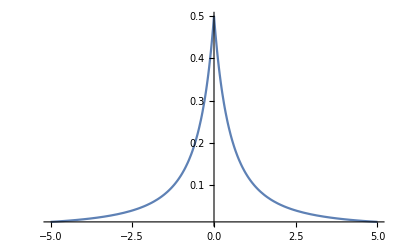

```mathematica
Plot[1/2 (1/(1+Abs[x])-Abs[x]/(1+Abs[x])^2),{x,-5,5},PlotRange->Full]
```

```mathematica
D[UnitStep[x]-Sign[x] 1/2(1-Abs[x]/(1+Abs[x]))^α,x]
```

(Piecewise[{{Indeterminate, x==0}, {0, True}}])-1/2 α (1-Abs[x]/(1+Abs[x]))^(-1+α) Sign[x] ((Abs[x] Abs'[x])/(1+Abs[x])^2-Abs'[x]/(1+Abs[x]))-1/2 (1-Abs[x]/(1+Abs[x]))^α Sign'[x]

```mathematica
Manipulate[Plot[1/2 α (1-Abs[x]/(1+Abs[x]))^(-1+α) (-(Abs@x)/(1+Abs[x])^2+1/(1+Abs[x])),{x,-5,5},PlotRange->{0,5}],{α,0,5}]
```

```mathematica
Manipulate[Plot[{Sign[x](2ArcTan[Abs[x]^(1+α)]/π)^(1/(1+α)),1/2((2/π)^(1/(1+α)) Abs[x]^α ArcTan[Abs[x]^(1+α)]^(-1+1/(1+α)))/(1+Abs[x]^(2(1+α)))},{x,-5,5}],{α,0,10}]
```

```mathematica
D[(2ArcTan[x^(1/α)]/π)^α,x]
```

((2/π)^α x^(-1+1/α) ArcTan[x^(1/α)]^(-1+α))/(1+x^(2/α))

```mathematica
-1+α-2α
```

-1-α

```mathematica
Solve[(2ArcTan[x^α]/π)^(1/α)==v,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→Tan[((π/2)^(1/α) v)^α]^(1/α)}}

```mathematica
Manipulate[Plot[Sign[2v-1] Tan[((π/2)^(1/(1+α)) Abs[2v-1])^(1+α)]^(1/(1+α)),{v,0,1}],{α,0,10}]
```

```mathematica
With[{α=1.5},NIntegrate[x^2 1/2((2/π)^(1/(1+α)) Abs[x]^α ArcTan[Abs[x]^(1+α)]^(-1+1/(1+α)))/(1+Abs[x]^(2(1+α))),{x,-Infinity,Infinity}]]
```

1.49191

```mathematica
((E^(I t)-1)/(I t))^n
```

(-(ⅈ (-1+ⅇ^(ⅈ t)))/t)^n

```mathematica
Integrate[((E^(I t)-1)/(I t))^n E^(-I t x),{t,-Infinity,Infinity},Assumptions->{n>1,Element[x,Reals]}]
```

$Aborted

```mathematica
(Normal@Series[Sinc[√3 t]^n,{t,0,10}])/.t->t/√n
```

1-t^2/2+(((3 n)/40+1/8 (-1+n) n) t^4)/n^2+((-(3 n)/560-3/80 (-1+n) n-1/48 (-2+n) (-1+n) n) t^6)/n^3+((n/4480+(123 (-1+n) n)/22400+3/320 (-2+n) (-1+n) n+1/384 (-3+n) (-2+n) (-1+n) n) t^8)/n^4+((-(3 n)/492800-(23 (-1+n) n)/44800-(93 (-2+n) (-1+n) n)/44800-1/640 (-3+n) (-2+n) (-1+n) n-((-4+n) (-3+n) (-2+n) (-1+n) n)/3840) t^10)/n^5

```mathematica
(Normal@Series[((E^(√3 I t)-E^(-√3 I t))/(2 √3 I t))^n,{t,0,10}])/.t->t/√n
```

1-t^2/2+(2^-n 3^(-n/2) (1/5 2^(-3+n) 3^(3/2+1/2 (-1+n)) n+2^(-3+n) 3^(1+1/2 (-2+n)) (-1+n) n) t^4)/n^2+1/n^3 2^-n 3^(-n/2) (-1/35 2^(-4+n) 3^(3/2+1/2 (-1+n)) n-1/5 2^(-4+n) 3^(2+1/2 (-2+n)) (-1+n) n-2^(-4+n) 3^(1/2+1/2 (-3+n)) (-2+n) (-1+n) n) t^6+1/n^4 2^-n 3^(-n/2) (1/35 2^(-7+n) 3^(1/2+1/2 (-1+n)) n+41/175 2^(-7+n) 3^(2+1/2 (-2+n)) (-1+n) n+1/5 2^(-6+n) 3^(5/2+1/2 (-3+n)) (-2+n) (-1+n) n+2^(-7+n) 3^(1+1/2 (-4+n)) (-3+n) (-2+n) (-1+n) n) t^8+1/n^5 2^-n 3^(-n/2) (-(2^(-8+n) 3^(3/2+1/2 (-1+n)) n)/1925-23/175 2^(-8+n) 3^(1+1/2 (-2+n)) (-1+n) n-31/175 2^(-8+n) 3^(5/2+1/2 (-3+n)) (-2+n) (-1+n) n-1/5 2^(-7+n) 3^(2+1/2 (-4+n)) (-3+n) (-2+n) (-1+n) n-1/5 2^(-8+n) 3^(3/2+1/2 (-5+n)) (-4+n) (-3+n) (-2+n) (-1+n) n) t^10

```mathematica
Solve[{1/2(a+b)==0,1/12(b-a)^2==1},{a,b}]
```

{{a→-√3,b→√3},{a→√3,b→-√3}}

```mathematica
1-(n t^2)/2+1/40 (-2 n+5 n^2) t^4/.t->t/√n
```

1-t^2/2+((-2 n+5 n^2) t^4)/(40 n^2)

```mathematica
Series[((3 n)/40+1/8 (-1+n) n)/n^2,{n,Infinity,10}]
```

1/8-1/(20 n)+O[1/n]^11

```mathematica
Series[Exp[-t^8],{t,0,10}]
```

1-t^8+O[t]^11

```mathematica
Integrate[Exp[-t^6] E^(-I t x),{t,-Infinity,Infinity},Assumptions->{x>0}]
```

-(4 π HypergeometricPFQ[{},{1/3,1/2,2/3,5/6},-x^6/46656])/Gamma[-1/6]-1/6 √π x^2 HypergeometricPFQ[{},{2/3,5/6,7/6,4/3},-x^6/46656]+(π x^4 HypergeometricPFQ[{},{7/6,4/3,3/2,5/3},-x^6/46656])/(216 Gamma[7/6])

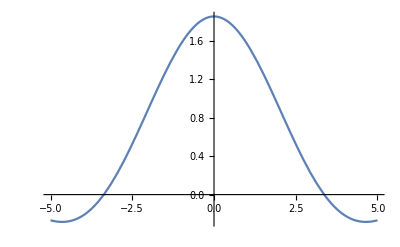

```mathematica
Plot[-(4 π HypergeometricPFQ[{},{1/3,1/2,2/3,5/6},-x^6/46656])/Gamma[-1/6]-1/6 √π x^2 HypergeometricPFQ[{},{2/3,5/6,7/6,4/3},-x^6/46656]+(π x^4 HypergeometricPFQ[{},{7/6,4/3,3/2,5/3},-x^6/46656])/(216 Gamma[7/6]),{x,-5,5}]
```

```mathematica
Series[((1-x^6)/(1-x))^n,{x,0,12}]//Simplify
```

1+n x+1/2 n (1+n) x^2+1/6 n (2+3 n+n^2) x^3+1/24 n (6+11 n+6 n^2+n^3) x^4+1/120 n (24+50 n+35 n^2+10 n^3+n^4) x^5+1/720 n (-600+274 n+225 n^2+85 n^3+15 n^4+n^5) x^6+(n (720-3276 n+1624 n^2+735 n^3+175 n^4+21 n^5+n^6) x^7)/5040+(n (5040-7092 n-7028 n^2+6769 n^3+1960 n^4+322 n^5+28 n^6+n^7) x^8)/40320+(n (40320-11376 n-63316 n^2+6804 n^3+22449 n^4+4536 n^5+546 n^6+36 n^7+n^8) x^9)/362880+(n (362880+119376 n-490500 n^2-183520 n^3+118125 n^4+63273 n^5+9450 n^6+870 n^7+45 n^8+n^9) x^10)/3628800+(n (3628800+2645280 n-3878424 n^2-3232900 n^3+90530 n^4+569415 n^5+157773 n^6+18150 n^7+1320 n^8+55 n^9+n^10) x^11)/39916800+(n (-199584000+280211040 n-31368744 n^2-44429924 n^3-10553070 n^4+3360335 n^5+1972278 n^6+357423 n^7+32670 n^8+1925 n^9+66 n^10+n^11) x^12)/479001600+O[x]^13

```mathematica
1/2
3/6
6/24
10/120
15/720
21/5040
```

1/2

1/2

1/4

1/12

1/48

1/240

```mathematica
diceOutcome[n_]:=1/6^n CoefficientList[((1-x^6)/(1-x)x)^n,x][[n+1;;]]
```

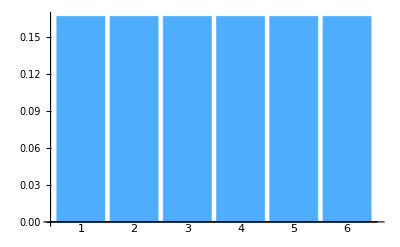

```mathematica
p1=With[{n=1},BarChart[diceOutcome[n],ChartLabels->Range[n,6n],LabelStyle->Directive[Black,Bold,12],ChartStyle->RGBColor[0.31,0.68,1.],TicksStyle->Directive[Black,Bold, 12]]]
Export["D:\\website\\CLT_plots\\dice1.png",p1,ImageResolution->100];
```

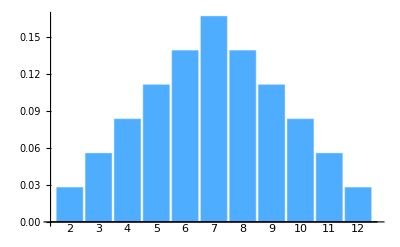

```mathematica
p2=With[{n=2},BarChart[diceOutcome[n],ChartLabels->Range[n,6n],LabelStyle->Directive[Black,Bold,12],ChartStyle->RGBColor[0.31,0.68,1.],TicksStyle->Directive[Black,Bold, 12]]]
Export["D:\\website\\CLT_plots\\dice2.png",p2,ImageResolution->100];
```

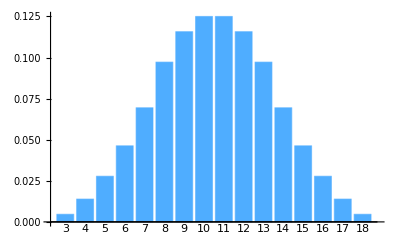

```mathematica
p3=With[{n=3},BarChart[diceOutcome[n],ChartLabels->Range[n,6n],LabelStyle->Directive[Black,Bold,12],ChartStyle->RGBColor[0.31,0.68,1.],TicksStyle->Directive[Black,Bold, 12]]]
Export["D:\\website\\CLT_plots\\dice3.png",p3,ImageResolution->100];
```

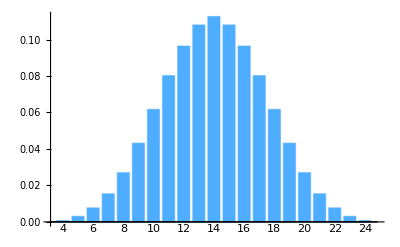

```mathematica
p4=With[{n=4},BarChart[diceOutcome[n],ChartLabels->Table[If[EvenQ@i,i,""],{i,n,6n}],LabelStyle->Directive[Black,Bold,12],ChartStyle->RGBColor[0.31,0.68,1.],TicksStyle->Directive[Black,Bold, 12]]]
Export["D:\\website\\CLT_plots\\dice4.png",p4,ImageResolution->100];
```

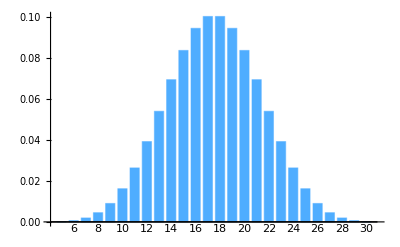

```mathematica
p5=With[{n=5},BarChart[diceOutcome[n],ChartLabels->Table[If[EvenQ@i,i,""],{i,n,6n}],LabelStyle->Directive[Black,Bold,12],ChartStyle->RGBColor[0.31,0.68,1.],TicksStyle->Directive[Black,Bold, 12]]]
Export["D:\\website\\CLT_plots\\dice5.png",p5,ImageResolution->100];
```

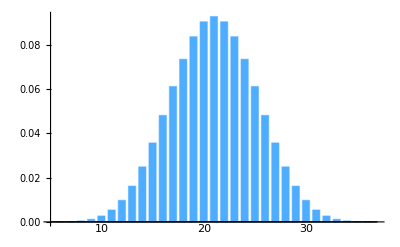

```mathematica
p6=With[{n=6},BarChart[diceOutcome[n],ChartLabels->Table[If[Mod[i,10]==0,i,""],{i,n,6n}],LabelStyle->Directive[Black,Bold,12],ChartStyle->RGBColor[0.31,0.68,1.],TicksStyle->Directive[Black,Bold, 12]]]
Export["D:\\website\\CLT_plots\\dice6.png",p6,ImageResolution->100];
```

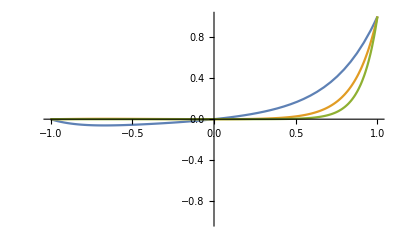

```mathematica
Plot[{1/6 x(1-x^6)/(1-x),1/6^2(x(1-x^6)/(1-x))^2,1/6^3(x(1-x^6)/(1-x))^3},{x,-1,1},PlotRange->{-1,1}]
```

```mathematica
SeriesCoefficient[((1-x^6)/(1-x))^n,{x,0,k}]
```

Piecewise[{{DifferenceRoot[Function[{y,n},{(n-5 n) y[n]+(1+n-4 n) y[1+n]+(2+n-3 n) y[2+n]+(3+n-2 n) y[3+n]+(4+n-n) y[4+n]+(5+n) y[5+n]==0,y[0]==1,y[1]==n,y[2]==1/2 n (1+n),y[3]==1/6 n (2+3 n+n^2),y[4]==1/24 n (6+11 n+6 n^2+n^3)}]][k], k≥0}, {0, True}}]

```mathematica
D[1/(1-x),{x,3}]
```

6/(1-x)^4

```mathematica
With[{n=5},D[1/((n-1)!)x^(n-1),{x,n-1}]]
With[{n=5},D[1/((n-1)!)x^n,{x,n-1}]]
With[{n=5},D[1/((n-1)!)x^(n+1),{x,n-1}]]
With[{n=5},D[1/((n-1)!)x^(n+2),{x,n-1}]]
With[{n=5},D[1/((n-1)!)x^(n+3),{x,n-1}]]
With[{n=5},D[1/((n-1)!)x^(n+4),{x,n-1}]]
```

1

5 x

15 x^2

35 x^3

70 x^4

126 x^5

```mathematica
D[x^n((1-x^6)/(1-x))^n,x]//Simplify
```

n x^(-1+n) (1+x+x^2+x^3+x^4+x^5)^(-1+n) (1+2 x+3 x^2+4 x^3+5 x^4+6 x^5)

```mathematica
1/6^n n x^(-1+n) (1+x+x^2+x^3+x^4+x^5)^(-1+n) (1+2 x+3 x^2+4 x^3+5 x^4+6 x^5)/.x->1
```

(7 n)/2

```mathematica
D[x D[x^n((1-x^d)/(1-x))^n,x],x]//Simplify
```

(n x^(-1+n) ((-1+x^d)/(-1+x))^n (x-d^2 x^d+2 (-1+d^2) x^(1+d)-d^2 x^(2+d)+x^(1+2 d)+n (1-(1+d) x^d+d x^(1+d))^2))/((-1+x)^2 (-1+x^d)^2)

```mathematica
Limit[(n x^(-1+n) ((-1+x^d)/(-1+x))^n (x-d^2 x^d+2 (-1+d^2) x^(1+d)-d^2 x^(2+d)+x^(1+2 d)+n (1-(1+d) x^d+d x^(1+d))^2))/((-1+x)^2 (-1+x^d)^2),x->1]
```

1/12 d^n (1+d) n (-1+d+3 n+3 d n)

```mathematica
1/d^n 1/12 d^n (1+d) n (-1+d+3 n+3 d n)-((d+1)/2 n)^2//Simplify
```

1/12 (-1+d^2) n

```mathematica
1/12 (-1+d^2) n
```

7/12 n (-21 n+6^n (5+21 n))

```mathematica
Series[(2+2 d^2+5 n-5 d^2 n)/(40 n-40 d^2 n),{n,Infinity,8}]//Simplify
Series[(-16 (1+d^2+d^4)+42 (-1+d^4) n-35 (-1+d^2)^2 n^2)/(1680 (-1+d^2)^2 n^2),{n,Infinity,8}]//Simplify
```

1/8+(1+d^2)/((20-20 d^2) n)+O[1/n]^9

-1/48+(1+d^2)/(40 (-1+d^2) n)-(1+d^2+d^4)/(105 (-1+d^2)^2 n^2)+O[1/n]^9

```mathematica
Series[1/6^n E^(I n t)((1-E^(6I t))/(1-E^(I t)))^n,{t,0,2}]
With[{μ=(d+1)/2 n,σ=√((d^2-1)/12 n)},Series[Exp[-I μ t/σ]/d^n E^(I n t/σ)((1-E^(d I t/σ))/(1-E^(I t/σ)))^n,{t,0,8}]]//FullSimplify
```

1+(7 ⅈ n t)/2-7/24 (5 n+21 n^2) t^2+O[t]^3

1-t^2/2+((2+2 d^2+5 n-5 d^2 n) t^4)/(40 n-40 d^2 n)+((-16 (1+d^2+d^4)+42 (-1+d^4) n-35 (-1+d^2)^2 n^2) t^6)/(1680 (-1+d^2)^2 n^2)+((-144 (1+d^2) (1+d^4)+4 (-101-21 d^2+21 d^4+101 d^6) n-420 (-1+d^2)^2 (1+d^2) n^2+175 (-1+d^2)^3 n^3) t^8)/(67200 (-1+d^2)^3 n^3)+O[t]^9

```mathematica
With[{μ=(d+1)/2 n,σ=√((d^2-1)/12 n)},Integrate[Exp[-I μ t/σ] E^(I n t/σ)/d^n((1-E^(dI t/σ))/(1-E^(I t/σ)))^n E^(-I t y),{t,-Infinity,Infinity},Assumptions->{n>1,Element[y,Reals]}]]
```

Integrate[6^-n ⅇ^(2 ⅈ √(3/35) √n t-ⅈ √(21/5) √n t-ⅈ t y) ((1-ⅇ^((12 ⅈ √(3/35) t)/(√n)))/(1-ⅇ^((2 ⅈ √(3/35) t)/(√n))))^n,{t,-∞,∞},Assumptions→{n>1,y∈ℝ}]

```mathematica
With[{μ=7/2 n,σ=√(35/12 n)},Simplify[Exp[-I μ t/σ] E^(I n t/σ)/6^n((1-E^(6I t/σ))/(1-E^(I t/σ)))^n]]
```

6^-n ⅇ^(-ⅈ √(15/7) √n t) (-(-1+ⅇ^((12 ⅈ √(3/35) t)/(√n)))/(1-ⅇ^((2 ⅈ √(3/35) t)/(√n))))^n

```mathematica
FullSimplify[Log[E^(I n t/σ)/6^n((1-E^(6I t/σ))/(1-E^(I t/σ)))^n],Assumptions->{n>1,Element[t,Reals]}]
```

Log[6^-n ⅇ^((ⅈ n t)/σ) (-(-1+ⅇ^((6 ⅈ t)/σ))/(1-ⅇ^((ⅈ t)/σ)))^n]

Table::iterb: Iterator {i,n,6 n} does not have appropriate bounds.

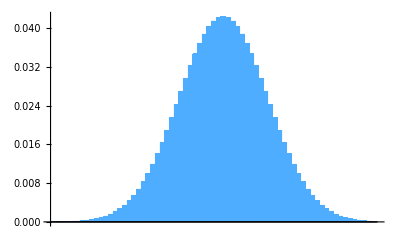

```mathematica
BarChart[data,ChartLabels->Table[If[Mod[i,15]==0,i,""],{i,n,6n}],LabelStyle->Directive[Black,Bold,12],ChartStyle->RGBColor[0.31,0.68,1.],TicksStyle->Directive[Black,Bold, 12]]
```

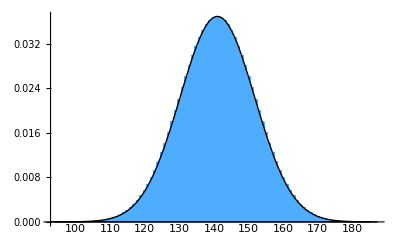

```mathematica
p=With[{n=40},
imin=Max[1,Floor[-n+7n/2-7 √n]];
imax=Min[Ceiling[-n+7n/2+7 √n],5n];
data=diceOutcome[n][[imin;;imax]];
Show[BarChart[data,ChartLabels->Table[If[Mod[imin+i,10]==0,imin+i,""],{i,n,6n}],LabelStyle->Directive[Black,Bold,12],ChartStyle->RGBColor[0.31,0.68,1.],TicksStyle->Directive[Black,Bold, 12]],Plot[1/(√(2π 35n/12))Exp[-(-2+n+imin+x-7n/2)^2/(2 35n/12)],{x,0,7n/2+7 √n-imin-n+2},PlotStyle->{Black,Thick}]]]
Export["D:\\website\\CLT_plots\\dice40.png",p,ImageResolution->100];
```